```mathematica
Clear["Global`*"];
```

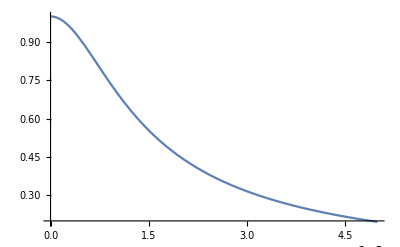

```mathematica
(*
Моделирование АЧХ фотодиода;
R||(C||CurrentGenerator);
Напряжение снимается с резистора;
Ток генератора = ASin[wt]
*)
J[A_,ω_,t_] := A Exp[I ω t];
Z[R_, ω_, c_]  := R/(I ω c) / (R + 1/(I ω c));
Solve[{J1+J2 == A,J1/(I ω c)== J2 R}, {J1, J2}];
R=1000; A = 0.001; c = 10*10^-12;
R J2/.%%[[1]];
Plot[Abs[%],{ω, 0, 5/(R c)}]
```

```mathematica
(*
На фотодиод подаём импусль длины τ, амплитудой 1 мА;
Необходимо перейти во временное пространство;
IR = Q/C, дифференцируем;
*)
Clear[j, j1,j2,R, c];

sol = DSolve[{HeavisideTheta[τ-t]== j1[t]+j2[t],D[j2[t], t] R== j1[t]/c , j2[0]==0}, {j1, j2}, t];
Plot[{(j2[t]/.sol[[1]]),j[t]}/.{R->1000,c -> 10*10^-12, τ->10^-9}, {t, 0, 10^-8}, MaxRecursion->6, PlotRange->All]
```

-Graphics-